# Diaphorina Network Model

## Single System Model

### Auxiliary Functions

```mathematica
ChartReport[init_,param1_,param2_,param3_,param4_]:=Transpose@Dataset[List@@@Normal[Dataset/@Association[
{"init"->Association@Thread[{"x1[0]","x2[0]","x3[0]","x4[0]","t"}->init]},
{"x1"->Association@Thread[{"r1","b12","b13","a1","c1"}->param1]},{"x2"->Association@Thread[{"r2","b21","b24","a2","c2"}->param2]},{"x3"->Association@Thread[{"r3","b31","a3","c3"}->param3]},{"x4"->Association@Thread[{"r4","b42","a4","c4"}->param4]}]]]
```

### System Equations

```mathematica
ClearAll[SystemEvolveNetwork];

Options[SystemEvolveNetwork] = {"LabelPosition" -> {0.88, 0.85}};

SystemEvolveNetwork[graph_,Dd_, Dt_,δ_, T_,{{r1_, b12_, b13_, a1_, c1_}, {r2_, b21_, b24_, a2_, c2_},{r3_, b31_, a3_, c3_},{r4_, b42_, a4_, c4_}},{Di0_, B0_, x30_, x40_, tt_},opts : OptionsPattern[]]:=Module[
{L, n,eqs,vars,ics,i, j},

L = Normal@KirchhoffMatrix[graph];
n = VertexCount[graph];
eqs = Flatten[{

(*---------------- Diaphorina ----------------*)

Table[
	x1[i]'[t] == x1[i][t]*(r1+b12*x2[i][t]+b13*x3[i][t]-(a1+c1*(b12*x2[i][t]+b13*x3[i][t]))*x1[i][t])- RandomReal[{5,10}]*Dd Sum[L[[i,j]] x1[j][t],{j,n}],
{i,n}],

(*---------------- Brotes ----------------*)

Table[
	x2[i]'[t] == x2[i][t]*(r2+b21*x1[i][t]+b24*x4[i][t]-(a2+c2*(b21*x1[i][t]+b24*x4[i][t]))*x2[i][t]),
{i,n}],

(*---------------- Tamarixia ----------------*)

Table[
	x3[i]'[t] ==x3[i][t]*(r3+b31*x1[i][t]-(a3+c3*b31*x1[i][t])*x3[i][t])- RandomReal[{5,10}]*Dt Sum[L[[i,j]] x3[j][t],{j,n}],
{i,n}],

(*---------------- Stimuli ----------------*)

Table[
	x4[i]'[t] == x4[i][t]*(r4+b42*x2[i][t]-(a4+c4*b42*x2[i][t])*x4[i][t]),
{i,n}]

}];


(*---------------- Condiciones iniciales ----------------*)

ics = Flatten[{

Table[x1[i][0] == Di0[[i]],{i,n}],

Table[x2[i][0] == B0[[i]],{i,n}],

Table[x3[i][0] == x30[[i]],{i,n}],

Table[x4[i][0] == x40[[i]],{i,n}]

}];


(*---------------- Liberación periódica ----------------*)


vars = Flatten[{

Table[x1[i],{i,n}],
Table[x2[i],{i,n}],
Table[x3[i],{i,n}],
Table[x4[i],{i,n}]

}];


eqs = NDSolve[Join[eqs, ics, {WhenEvent[Mod[t,T]==0 && t>0, Evaluate@Table[x3[i][t] -> x3[i][t] + δ,{i,n}]]}], vars, {t,0,tt}, Method->{"TimeIntegration"->"ExplicitRungeKutta"}];

Table[
	Plot[
	Evaluate[{x1[i][t],x2[i][t],x3[i][t],x4[i][t]}/.eqs],{t,0,tt},ImageSize->Medium,PlotLabel->"Node #"<>ToString@i,PlotLegends->Placed[{"Diaphorina citri","Plant shoots","Tamarixia radiata","Stimuli"},OptionValue["LabelPosition"]],PlotRange->All,FrameLabel->{"time (a.u.)","population"},GridLines->Automatic,GridLinesStyle->Directive[Dashed],Frame->True
	],
{i,1,n}]

]
```

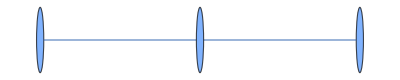

```mathematica
g=RandomGraph[{3, 2}]
```

```mathematica
n=VertexCount[g]
```

3

```mathematica
as=0.000555;cs=0.005;
param1={-0.2,0.04,-0.01,as,cs};
param2={-0.72,-0.01,0.054,as,cs};
param3={-0.3,0.01,as,cs};
param4={0.72,-0.072,as,cs};
init={{10,10,10},{10,10,10},{15,15,15},{40,40,40},100};
ChartReport[init,param1,param2,param3,param4]
```

```mathematica
sol=SystemEvolveNetwork[g,0.1,0.1,0,1,{param1,param2,param3,param4},init,"LabelPosition"->{0.8,0.8}];
```

0.120935 (x1[1][t]-x1[3][t])

0.1895 (x1[2][t]-x1[3][t])

0.146584 (-x1[1][t]-x1[2][t]+2 x1[3][t])

```mathematica
Dataset[Partition[sol,3]]
```

```mathematica
Manipulate[
Block[{sol=SystemEvolveNetwork[g,dd,dt,δ,10,{param1,param2,param3,param4},init,"LabelPosition"->{0.8,0.8}]},Dataset[Partition[sol,3]]],
{δ,0,100,10},
{dd,0,1,0.1},
{dt,0,1,0.1}
]
```